```mathematica
ImGlmt2Octet=0.02;
ImGlmt2Singlet=0.046;
```

```mathematica
Normalization=32/3;
AlphaS=0.108;
s=M^2;
Ch=beta0*Log[Mu^2/M^2]+CF*(Pi^2/3-8)+CA*(59/9+2*Log[2]/3-Pi^2/4)-10/9*nf*TF-16/9*TF;
CF=4/3;
CA=3;
TF=1/2;
nf=5;
beta0=(11/3)*CA-(4/3)*nf*TF;
Mu=mt;
mt=172.5; (* GeV *)
FHard=Normalization*Pi^2*AlphaS^2/(3*s)*(1+AlphaS*Ch/Pi)
```

2.62028×10^-6

```mathematica
invGeV2topb=0.389379*^9;
Luminosity=1018+1554+220+83+33;
Shadron=(2*6500)^2;
dxsect=Luminosity*M/Shadron*FHard*ImGlmt2Octet*invGeV2topb;
dxsect//.{M->360}
```

0.112672

```mathematica
Luminosity*M^2/Shadron*FHard
```

7.04308×10^-6 (1+0.0343775 (-11/3+4/3 (-8+π^2/3)+3 (59/9-π^2/4+(2 Log[2])/3)+23/3 Log[29756.3/M^2]))

```mathematica
(* gg > 1S_0^1 *)
Normalization=1;
Luminosity=55351;
Ch=beta0/2*Log[Mu^2/M^2]+CF*(Pi^2/4-5)+CA*(1+Pi^2/12);
FHard2to2=Normalization*Pi^2*AlphaS^2/(3*s)*(1+AlphaS/Pi*Ch);
M=2*mt;
LxF2to2=Luminosity*M^2/Shadron*FHard2to2
```

0.0000111752

```mathematica
func[z_]:=(1-z)*2*CA*(1/(1-z)+1/z+z*(1-z)-2)
```

((-5.99994+6 (1-z) (-2+1/(1-z)+1/z+(1-z) z)) Log[1-z])/(1-z)

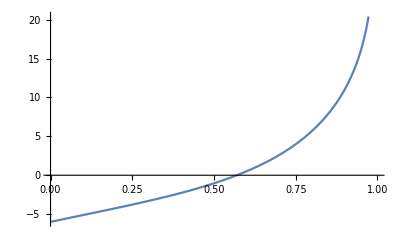

```mathematica
Log[1-z]/(1-z)*(func[z]-func[0.99999])
Plot[%,{z,0,0.9999}]
```

```mathematica
z/((1-z)^2*(1+z)^3)*(12+11*z^2+24*z^3-21*z^4-24*z^5+9*z^6-11*z^8+12*(-1+5*z^2+2*z^3+z^4+3*z^6+2*z^7)*Log[z]);
```

(12+11 z^2+24 z^3-21 z^4-24 z^5+9 z^6-11 z^8+12 (-1+5 z^2+2 z^3+z^4+3 z^6+2 z^7) Log[z])/((1-z)^2 z (1+z)^3)

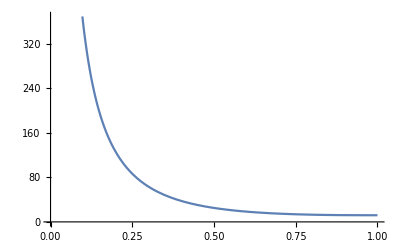

11+21 (-1+z)^2-152/5 (-1+z)^3+168/5 (-1+z)^4-1289/35 (-1+z)^5+1383/35 (-1+z)^6-1459/35 (-1+z)^7+652/15 (-1+z)^8-(103877 (-1+z)^9)/2310+3239/70 (-1+z)^10+z

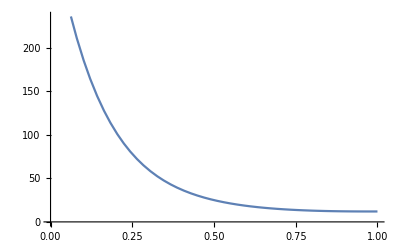

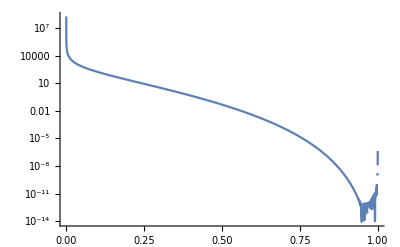

11 + 21*Power(-1 + z,2) - (152*Power(-1 + z,3))/5. + 
   (168*Power(-1 + z,4))/5. - (1289*Power(-1 + z,5))/35. + 
   (1383*Power(-1 + z,6))/35. - (1459*Power(-1 + z,7))/35. + 
   (652*Power(-1 + z,8))/15. - (103877*Power(-1 + z,9))/2310. + 
   (3239*Power(-1 + z,10))/70. + z

```mathematica
1/(z*(1-z)^2*(1+z)^3)*(12+11*z^2+24*z^3-21*z^4-24*z^5+9*z^6-11*z^8+12*(-1+5*z^2+2*z^3+z^4+3*z^6+2*z^7)*Log[z])
Plot[%,{z,0,0.99999}]
tmp=Normal[Series[%%,{z,1,10}]]
Plot[Normal[%],{z,0,1}]
LogPlot[Abs[%%%%-%%],{z,0.000001,0.99999},PlotRange->Full]
%%%//CForm
```

```mathematica
1/(z*(1-z)^2*(1+z)^3)*(12+11*z^2+24*z^3-21*z^4-24*z^5+9*z^6-11*z^8+12*(-1+5*z^2+2*z^3+z^4+3*z^6+2*z^7)*Log[z]);
Plot[%,{z,0,0.99999}]
tmp=Normal[Series[%%,{z,1,10}]]
Plot[Normal[%],{z,0,1}]
LogPlot[Abs[%%%%-%%],{z,0.000001,0.99999},PlotRange->Full]
%%%//CForm
```

-Graphics-

11+21 (-1+z)^2-152/5 (-1+z)^3+168/5 (-1+z)^4-1289/35 (-1+z)^5+1383/35 (-1+z)^6-1459/35 (-1+z)^7+652/15 (-1+z)^8-(103877 (-1+z)^9)/2310+3239/70 (-1+z)^10+z

-Graphics-

-Graphics-

11 + 21*Power(-1 + z,2) - (152*Power(-1 + z,3))/5. + 
   (168*Power(-1 + z,4))/5. - (1289*Power(-1 + z,5))/35. + 
   (1383*Power(-1 + z,6))/35. - (1459*Power(-1 + z,7))/35. + 
   (652*Power(-1 + z,8))/15. - (103877*Power(-1 + z,9))/2310. + 
   (3239*Power(-1 + z,10))/70. + z

```mathematica
mypow(1-z,2)*mypow(1+z,3))*(12+11*z2+24*z3-21*z4-24*z5+9*z6-11*z8+12*(-1+5*z2+2*z3+z4+3*z6+2*z7)*log(z)
```

(z (2+z+2 z^2-4 z^4-z^5+2 z^2 (5+2 z+z^2) Log[z]))/((1-z)^2 (1+z)^3)

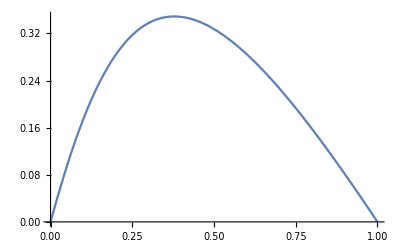

```mathematica
z/((1-z)^2*(1+z)^3)*(2+z+2*z^2-4*z^4-z^5+2*z^2*(5+2*z+z^2)*Log[z])
Plot[%,{z,0,0.99999}]
```

```mathematica
Integrate[Log[1-z]/(1-z)*(z^2-1),{z,0,1}]
```

7/4

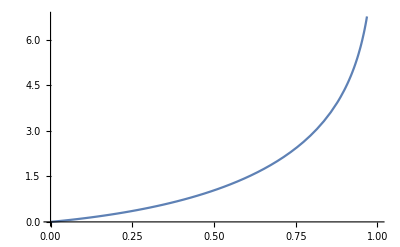

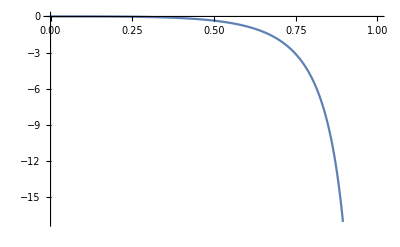

```mathematica
Plot[Log[1-z]/(1-z)*(z^2-1),{z,0,1}]
Plot[Log[1-z]/(1-z)*z^2,{z,0,1}]
```

```mathematica
Assuming[n>=1,Integrate[1/n!*(x-1)^(n-1),{x,0,1}]]
```

-(-1)^n/(n n!)

```mathematica
12+11+24-21-24+9-11
```

0

```mathematica
-1+5+2+1+3+2
```

12

```mathematica
Series[Log[]]
```

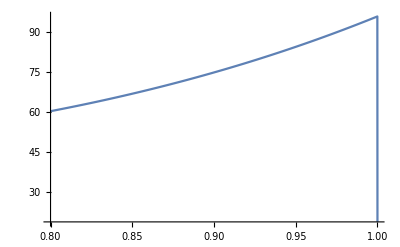

```mathematica
Plot[(12+11*z^2+24*z^3-21*z^4-24*z^5+9*z^6-11*z^8+12*(-1+5*z^2+2*z^3+z^4+3*z^6+2*z^7)*Log[z])/(1-z)^2,{z,0.8,1}]
```

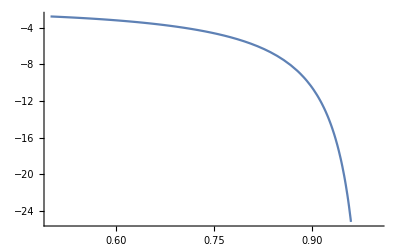

```mathematica
Plot[Log[x]/(1-x)^2,{x,0.5,1}]
```

```mathematica
-7.08854*^-8-1.24249*^-7-1.95651*^-8-1.18557*^-8-7.9324*^-9
%*1*^6
```

-2.34488×10^-7

-0.234488

```mathematica
-CA/(6*z*(1-z)^2*(1+z)^3)*(12+11*z2+24*z3-21*z4-24*z5+9*z6-11*z8+12*(-1+5*z2+2*z3+z4+3*z6+2*z7)*Log[z]);
%//.{z2->z^2,z3->z^3,z4->z^4,z5->z^5,z6->z^6,z7->z^7,z8->z^8}
Factor[Normal[Series[%,{z,1,20}]]]
```

-(CA (12+11 z^2+24 z^3-21 z^4-24 z^5+9 z^6-11 z^8+12 (-1+5 z^2+2 z^3+z^4+3 z^6+2 z^7) Log[z]))/(6 (1-z)^2 z (1+z)^3)

-1/116396280 CA (16726567988-198250312456 z+1316566775006 z^2-6050053993237 z^3+20820197762237 z^4-55960648779004 z^5+120586537417972 z^6-211905452110970 z^7+307072478889894 z^8-369434020871356 z^9+370208747826852 z^10-309045239447714 z^11+214269502709894 z^12-122594043492772 z^13+57272966854316 z^14-21497840744406 z^15+6328208451390 z^16-1407318191336 z^17+222356416026 z^18-22248986209 z^19+1060050445 z^20)

```mathematica
461*3
```

1383

(128 BF z (2+z+2 z^2-4 z^4-z^5+2 z^2 (5+2 z+z^2) Log[z]))/(3 CF Nc^2 (1-z)^2 (1+z)^3)

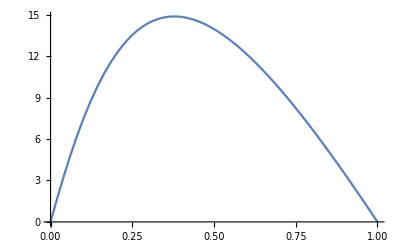

-(320 BF (-1+z))/(9 CF Nc^2)-(64 BF (-1+z)^2)/(9 CF Nc^2)+(448 BF (-1+z)^3)/(45 CF Nc^2)-(128 BF (-1+z)^4)/(15 CF Nc^2)+(608 BF (-1+z)^5)/(105 CF Nc^2)-(352 BF (-1+z)^6)/(105 CF Nc^2)+(224 BF (-1+z)^7)/(135 CF Nc^2)-(608 BF (-1+z)^8)/(945 CF Nc^2)+(1088 BF (-1+z)^9)/(10395 CF Nc^2)+(1472 BF (-1+z)^10)/(10395 CF Nc^2)

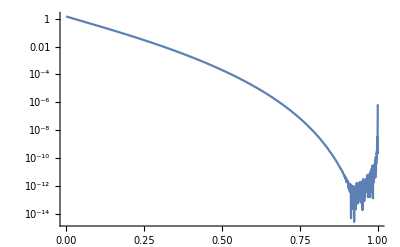

(128*BF*z*(2 + z + 2*z2 - 4*z4 - z5 + 2*z2*(5 + 2*z + z2)*log(z))*mypow(CF,-1)*mypow(Nc,-2)*mypow(1 - z,-2)*
     mypow(1 + z,-3))/3.

```mathematica
256*BF/(6*CF*Nc^2)*z/((1-z)^2*(1+z)^3)*(2+z+2*z^2-4*z^4-z^5+2*z^2*(5+2*z+z^2)*Log[z])
Plot[%//.{BF->1,CF->1,Nc->1},{z,0,1}]
Normal[Series[%%,{z,1,10}]]
LogPlot[Abs[%-%%%]//.{BF->1,CF->1,Nc->1},{z,0,1}]
%%%%//.{Power->mypow,Log->log,z^2->z2,z^3->z3,z^4->z4,z^5->z5}//CForm//.{Power->mypow}
```

(108+153 z+400 z^2+65 z^3-356 z^4-189 z^5-152 z^6-29 z^7+(108 z+756 z^2+432 z^3+704 z^4+260 z^5+76 z^6) Log[z])/(36 (1-z)^2 z (1+z)^3)

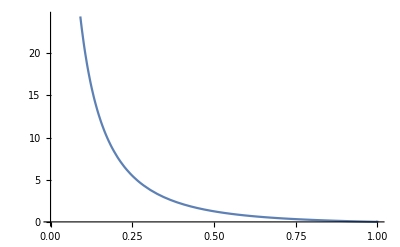

-95/108 (-1+z)+29/27 (-1+z)^2-487/270 (-1+z)^3+421/180 (-1+z)^4-337/126 (-1+z)^5+(3599 (-1+z)^6)/1260-(6665 (-1+z)^7)/2268+(67247 (-1+z)^8)/22680-(13204 (-1+z)^9)/4455+(92051 (-1+z)^10)/31185

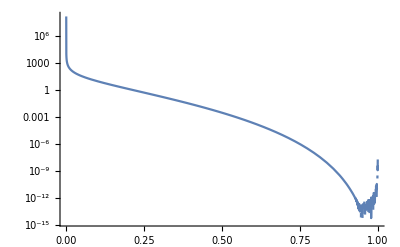

(-95*(-1 + z))/108. + (29*mypow(-1 + z,2))/27. - (487*mypow(-1 + z,3))/270. + (421*mypow(-1 + z,4))/180. - 
   (337*mypow(-1 + z,5))/126. + (3599*mypow(-1 + z,6))/1260. - (6665*mypow(-1 + z,7))/2268. + 
   (67247*mypow(-1 + z,8))/22680. - (13204*mypow(-1 + z,9))/4455. + (92051*mypow(-1 + z,10))/31185.

```mathematica
1/(36*z*(1-z)^2*(1+z)^3)*(108+153*z+400*z2+65*z3-356*z4-189*z5-152*z6-29*z7+(108*z+756*z2+432*z3+704*z4+260*z5+76*z6)*Log[z]);
%//.{z2->z^2,z3->z^3,z4->z^4,z5->z^5,z6->z^6,z7->z^7,z8->z^8}
Plot[%,{z,0,1}]
Normal[Series[%%,{z,1,10}]]
LogPlot[Abs[%-%%%],{z,0,1}]
%%//.{Power->mypow}//CForm
```

(AG x^bg)/(-1+ⅇ^(x/xbar))

(27.18 x^0.75)/(-1+ⅇ^(10.101 x))

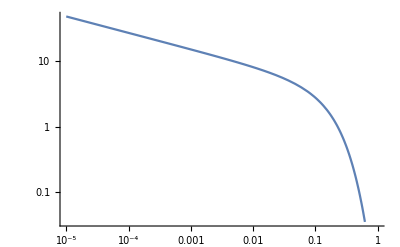

```mathematica
AG*x^bg/(Exp[x/xbar]-1)
%//.{AG->27.18,bg->0.75,xbar->0.099}
LogLogPlot[%,{x,1*^-5,1}]
```

```mathematica
11/3*3-4/3*5*1/2//N
```

7.66667

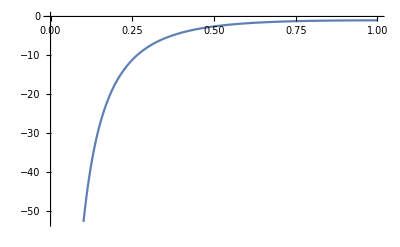

-CA-5/2 CA (-1+z)^2+11/6 CA (-1+z)^3-26/5 CA (-1+z)^4+28/5 CA (-1+z)^5-128/21 CA (-1+z)^6+229/35 CA (-1+z)^7-2179/315 CA (-1+z)^8+4553/630 CA (-1+z)^9-1647/220 CA (-1+z)^10

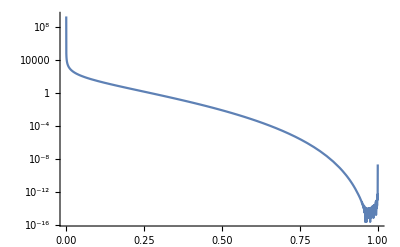

CA*(-1 - (5*mypow(-1 + z,2))/2. + (11*mypow(-1 + z,3))/6. - (26*mypow(-1 + z,4))/5. + (28*mypow(-1 + z,5))/5. - 
     (128*mypow(-1 + z,6))/21. + (229*mypow(-1 + z,7))/35. - (2179*mypow(-1 + z,8))/315. + 
     (4553*mypow(-1 + z,9))/630. - (1647*mypow(-1 + z,10))/220.)

```mathematica
-CA/(6*z*(1-z)*(1+z)^3)*(12+23*z^2+30*z^3-21*z^4-24*z^5+9*z^6-6*z^7-23*z^8+(-12+60*z^2+24*z^3+36*z^4+60*z^6+24*z^7)*Log[z]);
Plot[%//.{CA->1},{z,0,1}]
Normal[Series[%%,{z,1,10}]]
LogPlot[Abs[%-%%%]//.{CA->1},{z,0,1}]
Collect[%%//.{Power->mypow},CA|mypow[__]|log[__],Simplify]//CForm
Collect[%%%%%//.{Power->mypow,z^2->z2,z^3->z3,z^4->z4,z^5->z5,z^6->z6,z^7->z7,z^8->z8,Log->log},CA|mypow[__]|log[__],Simplify]//CForm;
```

```mathematica
Limit[-CA/(6*z*(1-z)*(1+z)^3)*(12+23*z^2+30*z^3-21*z^4-24*z^5+9*z^6-6*z^7-23*z^8+(-12+60*z^2+24*z^3+36*z^4+60*z^6+24*z^7)*Log[z]),z->1]
```

-CA

```mathematica
12+23+30-21
```

```mathematica
?Limit
```